```mathematica
(*http://openclassroom.stanford.edu/MainFolder/DocumentPage.php?course=DeepLearning&doc=exercises/ex2/ex2.html*)
```

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
import[fname_]:=ReadList[fname,String]//ImportString@@{#,"CSV"}&/@#&//Flatten
```

```mathematica
x=import["ex2x.dat"]//Map[List[1,#]&,#]&;
```

```mathematica
y=import["ex2y.dat"];
```

```mathematica
data =MapThread[List,{import["ex2x.dat"],y}];
```

```mathematica
{x//MatrixForm,y//MatrixForm}//Row
```

```mathematica
theta=Inverse[xᵀ.x].xᵀ.y
```

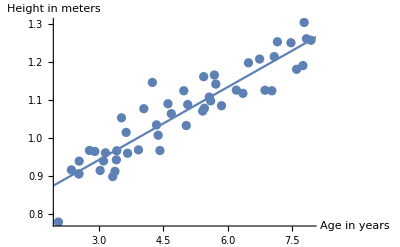

```mathematica
Show[ListPlot[data,AxesLabel->{"Age in years","Height in meters"}],
Plot[theta[[1]]+theta[[2]]*x,{x,0,10}]]
```